{0,0.01,0.0251189,0.0630957,0.158489,0.398107,1.,2.51189,6.30957,15.8489,39.8107,100.}

5.19118×10^-21

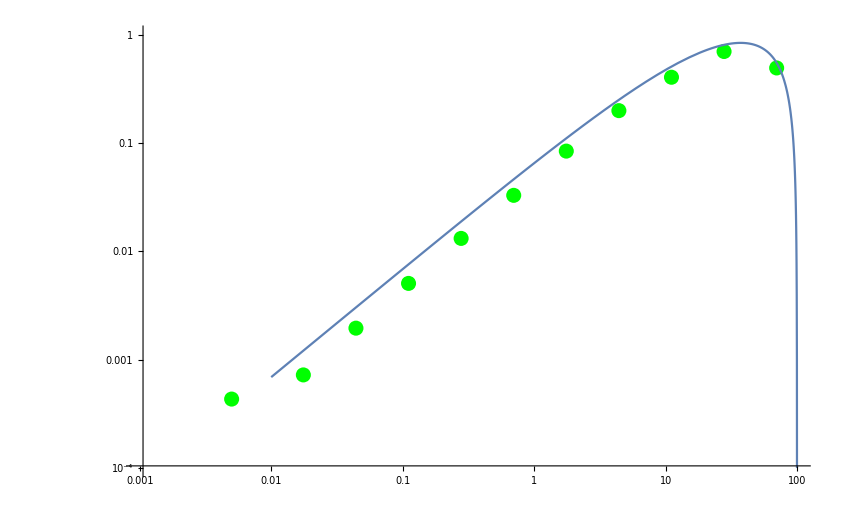

```mathematica
SetDirectory[NotebookDirectory[]];
tab=Import["specout4e","TSV"];
eflux=Import["eflux0"]//ToExpression;
tab=Flatten[tab,1]//ToExpression(*Imports photon spectrum for nevents in TeV*);
nevents=100000;
au=1.49598 10^11 *100;(*distance from earth to sun in cm*)
aum=1.49598 10^11 ;(*distance from earth to sun in m*)
SR=6.957 10^8;(*Solar radius in m*)
(*annin=Import["ann","Table"]//ToExpression;*)
annrate=eflux[[5]](*DM annihilation rate per second*);
minbin=0.01;
maxbin=100;
bincount=10;
maxheight=5 10^-11;
(*weights=Table[(tab[[i]])^2/nevents annrate/(4 π au^2),{i,1,Length[tab]}];*)
(*wtab=WeightedData[tab,weights];
Histogram[wtab,{"Log",bincount},"LogCount",PlotRange-> {{minbin,maxbin},{0,maxheight}}]*)
bins=Prepend[Table[10^li,{li,Log10[minbin],Log10[maxbin],(Log10[maxbin]-Log10[minbin])/bincount}],0]

(*bins={0.,0.5,1.6,5.0,15.7,50.0,158.1};*)
f[in_]:=Table[in>bins[[i]],{i,1,Length[bins]}];
tabsplit=SplitBy[tab,f[#]&];
dσIBdE[En_,mχ_]:=σtot α/(En π)(Log[(4mχ (mχ - En))/me^2]-1)(1+((4mχ (mχ-En))/(4 mχ^2))^2)/.{α-> 1/137.,me->0.511  10^-6(*TeV*),mμ-> 105.66 10^-6(*TeV*)};
dNdE[En_,mχ_]:=1/σtot dσIBdE[En,mχ]
E2dNdE[En_,mχ_]:=En^2 dNdE[En,mχ](*En and mχ are in TeV*)
(*LogLogPlot[E2dNdE[En,50],{En,0.01,100}]*)
(*Taken from 1503.01773*)
dNdx0[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1)(*x0 is 2*E0/m1, ϵf is 2 mf / m1, where E0 is energy of photon in rest frame of mediator 1 and m1 is mass of mediator 1*);
dNdx1[x1_,ϵ1_,ϵf_]:=(t1max=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1min=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0[x0,ϵf],{x0,t1min,t1max}])(*ϵ1 is 2 m1/m2 where m2 is the dark matter mass?, x1 = E1/m2 where E1 is the photon energy in the rest frame of dm. See end of pg 3 in 1503.01773*);
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA]
dNdE1μ[En_,mχ_,mA_]:=1/mχ dNdx1[En/mχ,(2mA)/mχ,(2*105.66 10^-6(*TeV*))/mA]
E2dNdE1e[En_,mχ_,mA_]:=En^2 dNdE1e[En,mχ,mA]
E2dNdE1μ[En_,mχ_,mA_]:=En^2 dNdE1μ[En,mχ,mA]
E2dNdE1tot[En_,mχ_,mA_]:=0.5 En^2 dNdE1e[En,mχ,mA]+0.5 En^2 dNdE1μ[En,mχ,mA]
(*Show[{LogLogPlot[E2dNdE1e[En,50.,0.5 10^-3],{En,0.01,100}],LogLogPlot[E2dNdE1μ[En,50.,0.5 10^-3],{En,0.01,100},PlotStyle->Red]}]*)
widthread=eflux[[9]]
τ=ℏ/(widthread (*GeV*) 10^9(*eV/GeV*))/.{ℏ-> 4.135667662 10^-15(*eV s*)};
γ=eflux[[1]]/eflux[[2]];
vel=c √(1-1/γ^2)/.{c-> 3 10^8(*m/s*)};
Pr[d_]:=Exp[-d/( vel γ τ )](*Probability it has survived by distance d*);
Prdetect=Pr[SR]-Pr[aum](*How many decay between the surface of the sun and the distance to earth*);
binnedtab=Table[{(bins⟦j⟧+bins⟦j+1⟧)/2,(1(*annrate*))/nevents(*1/(4π au^2)*) Sum[tabsplit[[j,i]],{i,1,Length[tabsplit⟦j⟧]}]},{j,1,Length[tabsplit]}];
HAWC=Log[{{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50.0,8.1 10^-14},{50.0,158.1,6.3 10^-14}}];
HAWCbinned=Table[{(Exp[HAWC[[i,2]]]+Exp[HAWC[[i,1]]])/2,eflux[[6,i]]/(Prdetect 1000.)},{i,1,5}];
HAWCLines=Table[{Red,Thick,Line[{{HAWC⟦i,1⟧,HAWC⟦i,3⟧},{HAWC⟦i,2⟧,HAWC⟦i,3⟧}}]},{i,1,Length[HAWC]}];
ListLogLogPlot[(*{*)binnedtab(*,HAWCbinned}*),PlotStyle-> {Blue,Green},PlotRange-> (*Automatic*){{0.001,100},{0.0001,1}}(*{{minbin,maxbin},{10^-19,maxheight}},Epilog-> HAWCLines*)];
Show[%,LogLogPlot[(*annrate*)(*1/(4π au^2)*)E2dNdE1tot[En,100.,0.5 10^-3],{En,0.01,100},PlotRange-> (*Automatic*){{0.001,100},{0.0001,1}}]]

(*Show[%,LogLogPlot[E2dNdE[En,50.],{En,0.01,100}],PlotRange->All]*)
```

```mathematica
binnedtab
```

{{0.005,0.000433208},{0.0175594,0.000723812},{0.0441073,0.0019557},{0.110793,0.00506346},{0.278298,0.0131763},{0.699054,0.0329084},{1.75594,0.0842618},{4.41073,0.19914},{11.0793,0.404989},{27.8298,0.699825},{69.9054,0.493315}}

```mathematica
01 6400 06 000000 T01 11 01
```